# Fix format of BHPC Mathematica PN amps.

## Set working directory and import Maple file

I’m storing the file “zlmkn8_ 5PN_e10.mx” in the same directory (folder) as this notebook so I set the working directory to the notebooks directory. Using latest data as of 26 March 2025 from https://sites.google.com/view/bhpc1996/data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/joshmathews/localgit/KerrEccentricEquatorialFigures/scripts/PN_amplitude_comparisons/5PN_e10_mathematica

Importing the Maple file. I don’t need to specify the pathway since the file is in the working directory. You can skip the previous step and just give the pathway to the file if you have it saved elsewhere.

```mathematica
MapleAmps=Import["zlmkn8_5PN_e10.mx"];
```

## Looking at the formatting of the imported data:

Mathematica reads the file in an odd manner; it thinks its a nested list;

```mathematica
MapleAmps[[0]]
```

List

```mathematica
Dimensions[MapleAmps]
```

{30508,4}

Each of the 30508 entries correspond to a given lmkn mode. That’s fine. For a given mode Mathematica thinks the entry is a list with 4 elements; {“string1”, m, k “string2”} where m and k are the mode numbers.

E . g .

```mathematica
InputForm[MapleAmps[[1]]]
```

{"zlmkn8[2", -1, 7, "10]=-3131497289341/283500*I*(1-Y^2)^(1/2)*e^10*Pi^(1/2)*(1+Y)^2*q^4*(-1+Y)^3*5^(1/2)*v^16+276637063274027/113\
4000*I*(1-Y^2)^(1/2)*e^10*Pi^(1/2)*(1+Y)^2*q^4*(-1+Y)^3*5^(1/2)*v^18;"}

```mathematica
Table[MapleAmps[[1]][[i]][[0]],{i,1,4}]
```

{String,Integer,Integer,String}

## Fixing the formatting:

Function to fix the formatting of a given lmkn mode entry and to define the output zlmkn8[l,m,k,n]. First it sticks the list together properly into a single string {“string1”, m, k “string2”}-> “string1, m, k string2” then evaluates the string as a Mathematica command.

```mathematica
fixformat[list_]:=ToExpression[StringRiffle[list,","]];
```

Now run the function on the full list of modes to define them in your Mathematica Kernel. This takes a moment and requires up to ~1GB RAM but works fine. The “Monitor” function displays the percentage of the modes completed.

```mathematica
imax=Dimensions[MapleAmps][[1]];
Monitor[Do[fixformat[MapleAmps[[i]]],{i,1,imax}],N[i/imax*100]]
```

## Evaluating the amplitudes

Now that it is finished; you can call a given mode and it returns the amplitude:

```mathematica
zlmkn8[5,3,4,7]
```

v^15 (-(6201722679677 ⅈ e^7 √(π/66) q^2 (-1+Y)^2 (1+Y)^5)/184320+(129698743641019 ⅈ e^9 √(π/66) q^2 (-1+Y)^2 (1+Y)^5)/184320)+v^17 ((17462195812182779 ⅈ e^7 √(π/66) q^2 (-1+Y)^2 (1+Y)^5)/28753920-(15590257291103631577 ⅈ e^9 √(π/66) q^2 (-1+Y)^2 (1+Y)^5)/1150156800)+v^18 (1/5529600 117649 e^7 √(π/66) q^2 (-1+Y)^2 (1+Y)^5 (-97836762688+44279569320 EulerGamma-22139784660 ⅈ π-23350016889 ⅈ q-22139784660 √(1-q^2)+62029242765 ⅈ q Y)-1/44236800 117649 e^9 √(π/66) q^2 (-1+Y)^2 (1+Y)^5 (-17542790105344+7939624832160 EulerGamma-3969812416080 ⅈ π-4394109175317 ⅈ q-3969812416080 √(1-q^2)+11697722150835 ⅈ q Y))

And you can evaluate it for a given set of parameters;

```mathematica
zlmkn8[5,3,4,7]/.{e->1/2,q->0.2,v->0.3,Y->Cos[π/4]}
```

0.000302354+0.0000782432 ⅈ

Yay.

If a given mode ‘doesn’t work’ it’s because it was excluded from the Maple data anyway.

E.g. This doesn’t evaluate:

```mathematica
zlmkn8[5,3,4,13]
```

zlmkn8[5,3,4,13]

# Amp data for comparing Equatorial Kerr FEW.

## Note on typos in 5PN public data.

Soichiro’s email 26/03/2025:

“The point is that, up to 5PN (the spheroidal mode up to ell = 10), the typos
in BHPC’s public 5PN amplitudes data are following.

1. We have to invert the overall sign for the modes m = 3, 5, 7, 9, 11,
whatever the values of ell, k and n are (ie multiply by (-1) ).
2. All m = 0 modes (for arbitrary mode numbers of ell, k, n) have typos,
but only in the 5PN term. The explicit expressions for each difference
are in (my) Maple, but they haven’t yet been transferred to Mma and C.”

Since we can compare the spherical mode amplitudes for even values of m greater than zero, we can avoid these typos.

## Equatorial k=0 modes

Use KerrGeodesics package to compute LSO.  https://bhptoolkit.org/KerrGeodesics/ . Set δp=p-pLSO. v=√(1/p)=√(1/(pLSO(a,e,x)+δp))

```mathematica
<<Teukolsky`
```

```mathematica
zlmnEquatorialfromsep[l_,m_,n_,a_,δp_,ee_,x_]:=zlmkn8[l,m,0,n]/.{v->√(1/(KerrGeoSeparatrix[a,ee,x]+δp)),Y->1, q->x*a (*BHPC convention pro/retrograde in equatorial plane*),e->ee};
```

```mathematica
zlmnEquatorial[l_,m_,n_,a_,p_,ee_,x_]:=zlmkn8[l,m,0,n]/.{v->√(1/p),Y->1, q->x*a (*BHPC convention pro/retrograde in equatorial plane*),e->ee};
```

```mathematica
extraphasefactor[m_,n_, a_,p_,ee_,x_]:=Module[{bincphase,ωmkn,rm,Ωr,Ωϕ},

rm=1-√(1-a^2);

Ωr=KerrGeoFrequencies[a,p,ee,x]["Ω_r"];
Ωϕ=KerrGeoFrequencies[a,p,ee,x]["Ω_ϕ"];

ωmkn=m*Ωϕ+n*Ωr;

bincphase=-ωmkn*(2*Log[2* ωmkn]-rm)-2*ωmkn*Log[2];

Exp[-I bincphase]];
```

```mathematica
ZlmnEquatorialfromsep[l_,m_,n_,a_,δp_,ee_,x_]:=(-1)^(n+1)zlmnEquatorialfromsep[l,m,n,a,δp,ee,x]*extraphasefactor[m,n, a,KerrGeoSeparatrix[a,ee,x]+δp,ee,x];
ZlmnEquatorial[l_,m_,n_,a_,p_,ee_,x_]:=(-1)^(n+1)zlmnEquatorial[l,m,n,a,p,ee,x]*extraphasefactor[m,n, a,p,ee,x];
```

Extra phase factor above - see readme. Factor of (-1)^(n+1) for initial phase convention.

```mathematica
Strainamp[l_,m_,n_,a_,p_,ee_,x_]:=Module[{amp,ωmkn,rm,Ωr,Ωϕ},

Ωr=KerrGeoFrequencies[a,p,ee,x]["Ω_r"];
Ωϕ=KerrGeoFrequencies[a,p,ee,x]["Ω_ϕ"];

ωmkn=m*Ωϕ+n*Ωr;

amp=-2*ZlmnEquatorial[l,m,n,a,p,ee,x]/(I*ωmkn)^2;

amp];
```

```mathematica
StrainampNumeric[l_,m_,n_,a_,p_,ee_,x_]:=Module[{amp,ωmkn,rm,Ωr,Ωϕ},

Ωr=KerrGeoFrequencies[a,p,ee,x]["Ω_r"];
Ωϕ=KerrGeoFrequencies[a,p,ee,x]["Ω_ϕ"];

ωmkn=m*Ωϕ+n*Ωr;

amp=-2*(TeukolskyPointParticleMode[-2,l,m,n,0,KerrGeoOrbit[a,N[p],ee,x]]["Amplitudes"]["ℐ"])/(I*ωmkn)^2;

amp];
```

```mathematica
Strainampfromsep[l_,m_,n_,a_,δp_,ee_,x_]:=Module[{amp,ωmkn,rm,Ωr,Ωϕ,psep},

psep=KerrGeoSeparatrix[a,ee,x];

Ωr=KerrGeoFrequencies[a,psep+δp,ee,x]["Ω_r"];
Ωϕ=KerrGeoFrequencies[a,psep+δp,ee,x]["Ω_ϕ"];

ωmkn=m*Ωϕ+n*Ωr;

amp=-2*ZlmnEquatorialfromsep[l,m,n,a,δp,ee,x]/(I*ωmkn)^2;

amp];
```

#### Checking against toolkit:

```mathematica
testteuk=TeukolskyPointParticleMode[-2,2,2,0,0,KerrGeoOrbit[0.9,N[100],0.19,1]]["Amplitudes"]["ℐ"]
```

-9.73585×10^-8+2.10863×10^-9 ⅈ

```mathematica
testPN=ZlmnEquatorial[2,2,0,0.9,N[100],0.19,1]
```

-9.73585×10^-8+2.10863×10^-9 ⅈ

```mathematica
1-testteuk/testPN
```

-3.05957×10^-8-3.03862×10^-9 ⅈ

```mathematica
Strainamp[2,2,0,0.01,N[100],0.01,1]
```

-0.0621404+0.00140805 ⅈ

```mathematica
StrainampNumeric[2,2,0,0.1,10,0.1,1]
```

-0.52195+0.141544 ⅈ

```mathematica
SpinWeightedSpheroidalHarmonicS[-2,2,2,0.01*(2*KerrGeoFrequencies[0.01,N[100],0.01,1]["Ω_ϕ"]),Method->"SphericalExpansion"]["ExpansionCoefficients"]
```

SpinWeightedSpheroidalHarmonicS::numterms: Automatic determination of the number of terms to use in the SphericalExpansion method may be unreliable in certain cases. Currently using 6 terms. It is recommended to verify the result is unchanged with a different number of terms.

<|2→1.,3→3.75565×10^-6,4→1.11515×10^-11,5→2.56717×10^-17,6→4.87586×10^-23,7→7.80624×10^-29,8→1.08307×10^-34|>

```mathematica
-StrainampNumeric[2,2,0,0.9,100,0.15,1]
```

0.0571745-0.00125956 ⅈ

## Data for plots

Generate two data sets for lmn=220 and 221 modes:
1. A plot varying over a and e for large p. say p=100.
2 A plot in the p and e plane for lower p values at given values of a.  Phil’s flux plot is on the grid: ps = np.linspace(40, 200, 50), es = np.linspace(0.01, 0.9, 50) and set a=0.998.
3. Repeat plot 2 but in strong field for my own curiosity.

Want the strain amp not the Teukolsky amp (Eq.77 Pound +Wardell):

### Data for plot 1

```mathematica
Plot1es=Range[0.01,0.9,(0.9-0.01)/(50-1)];
Plot1as=Range[0.01,0.9,(0.9-0.01)/(50-1)];
```

```mathematica
plot1modedata[l_,m_,n_,p_,x_]:=Flatten[Table[{Plot1es[[i]], Plot1as[[j]], Re[Strainamp[l,m,n, Plot1as[[j]],p, Plot1es[[i]],x]], Im[Strainamp[l,m,n,Plot1as[[j]],p, Plot1es[[i]],x]]},{i,1,Length[Plot1es]},{j,1,Length[Plot1as]}],1];
```

#### n=0 modes

```mathematica
p1l2m2n0=plot1modedata[2,2,0,100,1];
p1l3m2n0=plot1modedata[3,2,0,100,1];
p1l4m2n0=plot1modedata[4,2,0,100,1];
p1l5m2n0=plot1modedata[5,2,0,100,1];
p1l6m2n0=plot1modedata[6,2,0,100,1];
```

```mathematica
Export["p1l2m2n0.csv",p1l2m2n0]
Export["p1l3m2n0.csv",p1l3m2n0]
Export["p1l4m2n0.csv",p1l4m2n0]
Export["p1l5m2n0.csv",p1l5m2n0]
Export["p1l6m2n0.csv",p1l6m2n0]
```

p1l2m2n0.csv

p1l3m2n0.csv

p1l4m2n0.csv

p1l5m2n0.csv

p1l6m2n0.csv

#### n=1 modes

```mathematica
p1l2m2n1=plot1modedata[2,2,1,100,1];
p1l3m2n1=plot1modedata[3,2,1,100,1];
p1l4m2n1=plot1modedata[4,2,1,100,1];
p1l5m2n1=plot1modedata[5,2,1,100,1];
p1l6m2n1=plot1modedata[6,2,1,100,1];
```

```mathematica
Export["p1l2m2n1.csv",p1l2m2n1]
Export["p1l3m2n1.csv",p1l3m2n1]
Export["p1l4m2n1.csv",p1l4m2n1]
Export["p1l5m2n1.csv",p1l5m2n1]
Export["p1l6m2n1.csv",p1l6m2n1]
```

p1l2m2n1.csv

p1l3m2n1.csv

p1l4m2n1.csv

p1l5m2n1.csv

p1l6m2n1.csv

### Data for Plot 2

```mathematica
Plot2ps=N[Range[40,200,(200-40)/(50-1)]];
Plot2es=N[Range[0.01,0.9,(0.9-0.01)/(50-1)]];
```

```mathematica
plot2modedata[l_,m_,n_,a_,x_]:=Flatten[Table[{Plot2ps[[i]], Plot2es[[j]], Re[Strainamp[l,m,n,a,Plot2ps[[i]], Plot2es[[j]],x]], Im[Strainamp[l,m,n,a,Plot2ps[[i]], Plot2es[[j]],x]]},{i,1,Length[Plot2ps]},{j,1,Length[Plot2es]}],1];
```

#### n=0 modes

```mathematica
p2l2m2n0=plot2modedata[2,2,0,0.998,1];
p2l3m2n0=plot2modedata[3,2,0,0.998,1];
p2l4m2n0=plot2modedata[4,2,0,0.998,1];
p2l5m2n0=plot2modedata[5,2,0,0.998,1];
p2l6m2n0=plot2modedata[6,2,0,0.998,1];
```

```mathematica
Export["p2l2m2n0.csv",p2l2m2n0]
Export["p2l3m2n0.csv",p2l3m2n0]
Export["p2l4m2n0.csv",p2l4m2n0]
Export["p2l5m2n0.csv",p2l5m2n0]
Export["p2l6m2n0.csv",p2l6m2n0]
```

p2l2m2n0.csv

p2l3m2n0.csv

p2l4m2n0.csv

p2l5m2n0.csv

p2l6m2n0.csv

#### n=1 modes

```mathematica
p2l2m2n1=plot2modedata[2,2,1,0.998,1];
p2l3m2n1=plot2modedata[3,2,1,0.998,1];
p2l4m2n1=plot2modedata[4,2,1,0.998,1];
p2l5m2n1=plot2modedata[5,2,1,0.998,1];
p2l6m2n1=plot2modedata[6,2,1,0.998,1];
```

```mathematica
Export["p2l2m2n1.csv",p2l2m2n1]
Export["p2l3m2n1.csv",p2l3m2n1]
Export["p2l4m2n1.csv",p2l4m2n1]
Export["p2l5m2n1.csv",p2l5m2n1]
Export["p2l6m2n1.csv",p2l6m2n1]
```

p2l2m2n1.csv

p2l3m2n1.csv

p2l4m2n1.csv

p2l5m2n1.csv

p2l6m2n1.csv

### Data for Plot 3

```mathematica
Plot3deltaps=N[Range[1,30,(29)/(50-1)]];
Plot3es=N[Range[0.01,0.9,(0.9-0.01)/(50-1)]];
```

```mathematica
plot3modedata[l_,m_,n_,a_,x_]:=Flatten[Table[{Plot3deltaps[[i]], Plot3es[[j]], Re[Strainampfromsep[l,m,n,a,Plot3deltaps[[i]], Plot3es[[j]],x]], Im[Strainampfromsep[l,m,n,a,Plot3deltaps[[i]], Plot3es[[j]],x]]},{i,1,Length[Plot3deltaps]},{j,1,Length[Plot3es]}],1];
```

#### n=0 modes

```mathematica
p3l2m2n0=plot3modedata[2,2,0,0.998,1];
p3l3m2n0=plot3modedata[3,2,0,0.998,1];
p3l4m2n0=plot3modedata[4,2,0,0.998,1];
p3l5m2n0=plot3modedata[5,2,0,0.998,1];
p3l6m2n0=plot3modedata[6,2,0,0.998,1];
```

```mathematica
Export["p3l2m2n0.csv",p3l2m2n0]
Export["p3l3m2n0.csv",p3l3m2n0]
Export["p3l4m2n0.csv",p3l4m2n0]
Export["p3l5m2n0.csv",p3l5m2n0]
Export["p3l6m2n0.csv",p3l6m2n0]
```

p3l2m2n0.csv

p3l3m2n0.csv

p3l4m2n0.csv

p3l5m2n0.csv

p3l6m2n0.csv

#### n=1 modes

```mathematica
p3l2m2n1=plot3modedata[2,2,1,0.998,1];
p3l3m2n1=plot3modedata[3,2,1,0.998,1];
p3l4m2n1=plot3modedata[4,2,1,0.998,1];
p3l5m2n1=plot3modedata[5,2,1,0.998,1];
p3l6m2n1=plot3modedata[6,2,1,0.998,1];
```

```mathematica
Export["p3l2m2n1.csv",p3l2m2n1]
Export["p3l3m2n1.csv",p3l3m2n1]
Export["p3l4m2n1.csv",p3l4m2n1]
Export["p3l5m2n1.csv",p3l5m2n1]
Export["p3l6m2n1.csv",p3l6m2n1]
```

p3l2m2n1.csv

p3l3m2n1.csv

p3l4m2n1.csv

p3l5m2n1.csv

p3l6m2n1.csv

### Toolkit validation of plot 2:

```mathematica
plot2modedatatoolkit[l_,m_,n_,a_,x_]:=Flatten[Table[{Plot2ps[[i]], Plot2es[[j]], StrainampNumeric[l,m,n,a,Plot2ps[[i]], Plot2es[[j]],x]},{i,1,Length[Plot2ps]},{j,1,Length[Plot2es]}],1];
```

```mathematica
p2l2m2n0toolkit=Monitor[plot2modedatatoolkit[2,2,0,0.998,1],{Length[Plot2ps]-i,Length[Plot2es]-j}];
```

```mathematica
Rereldiffs=Table[{p2l2m2n0toolkit[[i]][[1]],p2l2m2n0toolkit[[i]][[2]],Log10[Abs[1-Re[p2l2m2n0toolkit[[i]][[3]]]/p2l2m2n0[[i]][[3]]] ]},{i,1,Length[p2l2m2n0toolkit]}];
```

```mathematica
Imreldiffs=Table[{p2l2m2n0toolkit[[i]][[1]],p2l2m2n0toolkit[[i]][[2]],Log10[Abs[1-Im[p2l2m2n0toolkit[[i]][[3]]]/p2l2m2n0[[i]][[4]]] ]},{i,1,Length[p2l2m2n0toolkit]}];
```

```mathematica
Imreldiffsfiltered=DeleteCases[Imreldiffs,{_,_,x_}/;!NumericQ[x]];
Rereldiffsfiltered=DeleteCases[Rereldiffs,{_,_,x_}/;!NumericQ[x]];
```

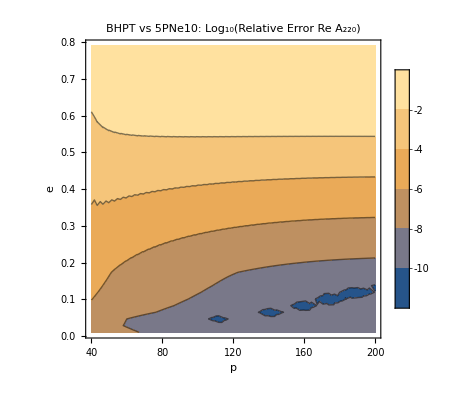

```mathematica
recomparison=ListContourPlot[Rereldiffsfiltered,PlotLegends->Automatic,FrameLabel->{p,e},FrameStyle->Directive[Black,Medium],PlotLabel->"BHPT vs 5PNe10: Log_10(Relative Error Re A_220)"]
```

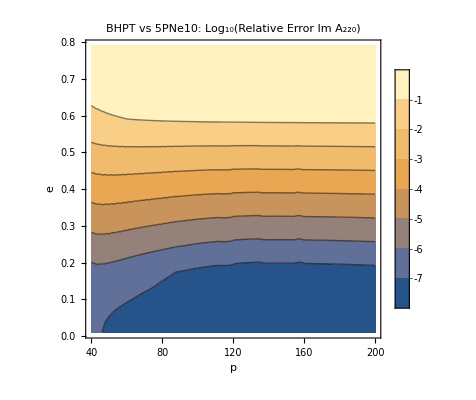

```mathematica
imcomparison=ListContourPlot[Imreldiffsfiltered,PlotLegends->Automatic,PlotRange->All,PlotLabel->Style["BHPT vs 5PNe10: Log_10(Relative Error Im A_220)",Black],FrameLabel->{p,e},FrameStyle->Directive[Black,Medium]]
```

```mathematica
Export["ImA220BhptVS5PN.pdf",imcomparison]
```

ImA220BhptVS5PN.pdf

```mathematica
Export["ReA220BhptVS5PN.pdf",recomparison]
```

ReA220BhptVS5PN.pdf